```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/blogit" ]
```

/Users/pjoot/project/figures/blogit

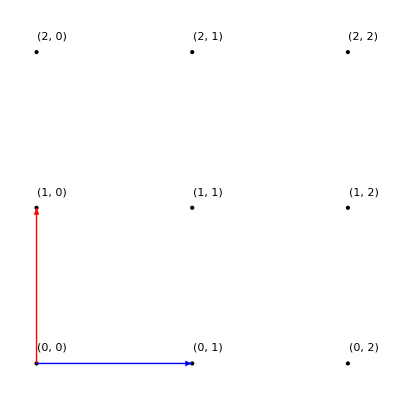

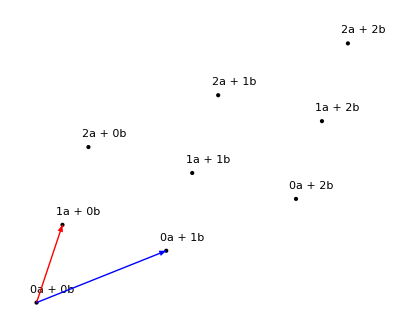

```mathematica
ClearAll[o,lattice,rect,oblique]
o = {0,0};

lattice[a_, b_, r_] := Graphics[
{
Table[Point[n a + m b],{n,0,r},{m,0,r}],
Table[Text[Row[{"(", n, ", ", m, ")"}],(n + 0.1) a + (m + 0.1) b],{n,0,r},{m,0,r}],
Red,
Arrow[{o,a}],
Blue,
Arrow[{o,b}]
}
]

lattice2[a_, b_, r_] := Graphics[
{
Table[Point[n a + m b],{n,0,r},{m,0,r}],
Table[Text[Row[{ n, Style["a",Bold], " + ", m, Style["b", Bold]}],(n + 0.1) a + (m + 0.1) b],{n,0,r},{m,0,r}],
Red,
Arrow[{o,a}],
Blue,
Arrow[{o,b}]
}
]

rect = lattice[{0,1},{1,0}, 2]
oblique = lattice2[{1,3}, {5,2}, 2]
```

```mathematica
peeters`exportForLatex["rectFig1", rect] 
peeters`exportForLatex["obliqueFig2", oblique]
```

{rectFig1.eps,rectFig1pn.png}

{obliqueFig2.eps,obliqueFig2pn.png}